```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190226_fixed_TL_cy3_accum_15h/TL*.tif"];
```

```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_NT_*/NT*.tif" ];
```

```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_TL_*/TL*.tif" ];
```

```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_TA_*/TA*.tif" ];
```

```mathematica
myFileNames = FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/20190226_fixed_TL_cy3_accum_15h/TL*"];
```

```mathematica
myFiles = Import/@myFileNames;
```

```mathematica
ImageAdjust/@myFiles[[1]]
```

```mathematica
mymeanlist = Mean/@myFiles[[2;;All,1]];
```

```mathematica
Length@myFiles-1
```

100

```mathematica
meanImgs= Sort[Table[Thread[{ mymeanlist[[i]],myFiles[[2;;All,1]][[i]] }] , {i,1,Length@myFiles-1}] ] ;
```

```mathematica
meanImgs100Sorted = RandomChoice[meanImgs,100]//Sort//#[[All,2]]&;
```

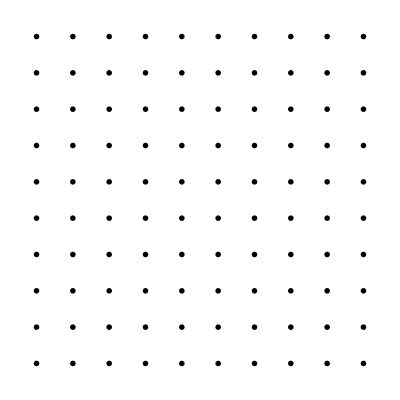

```mathematica
myCellsGsorted = Table[ImageResize[ImageAdjust[meanImgs100Sorted[[img]],{1,2,1},{.0001,.2}],{64,64}],{img,1,100,1}];
GraphicsGrid[Partition[myCellsGsorted,10]]
```

```mathematica
ImageResize[-Graphics-,{64,64}];
```

```mathematica
myCellsG = Table[ImageResize[ImageAdjust[myFiles[[img,1]],{1,2,1},{.0001,.2}],{64,64}],{img,2,101,1}];
GraphicsGrid[Partition[myCellsG,10]]
```

-Graphics-

```mathematica
myCellsG = Table[ImageResize[ImageAdjust@myFiles[[img,1]],{64,64}],{img,1,101,1}];
gridG=GraphicsGrid[Partition[myCellsG,10]]
```

-Graphics-

```mathematica
myCellsB = Table[ImageResize[
ImageAdjust[myFiles[[img,2]],{1,1,1},{.00001,.075}],{64,64}],{img,1,100,1}];
gridB=GraphicsGrid[Partition[myCellsB,10]]
```

-Graphics-

```mathematica
dummyImg = Flatten[Table[Flatten@Table[0,1,64],1,64],1]//Image
dummyImgW = Flatten[Table[Flatten@Table[1,1,64],1,64],1]//Image
dummyImg//ImageDimensions
```

-Graphics-

-Graphics-

{64,64}

```mathematica
dummyImgs =GraphicsGrid[  Partition[Table[-Graphics-,100],10]  ];
```

```mathematica
ColorNegate[(myCellsG[[1]]+ myCellsB[[1]])/.5]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[ Table[ColorCombine[{myCellsB[[i]], myCellsG[[i]], dummyImg,ColorNegate[(myCellsG[[i]]+ myCellsB[[i]])/2]},"CMYK"],  {i,1,100}],10]]
```

-Graphics-

```mathematica
myTable = ColorCombine[{dummyImgs,gridG,gridB}]
```

-Graphics-

```mathematica
myFileNames[[1]]
```

/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190301_TL_fix_transf_cy3-flag-fab_accum/TL00.tif

```mathematica
(*Export[ "/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/G_TL1_grid.tif"  ,tl1accumgrid]
```